```mathematica
SWINGING MASS FROM A CHANGING STRING:

P=1/2*m*(Subscript[l, 0]+α*t)^2*(Sin[θ[t]])^2*(ϕ'[t])^2+1/2*m*(Subscript[l, 0]+α*t)^2*(θ'[t])^2+m*g*(Subscript[l, 0]+α*t)*Cos[θ[t]]
D[(D[P,θ'[t]]), t]-D[P,θ[t]]
D[(D[P,ϕ'[t]]), t]-D[P,ϕ[t]]
```

2. Cos[θ[t]]+0.2 θ'[t]^2+0.2 Sin[θ[t]]^2 ϕ'[t]^2

2. Sin[θ[t]]-0.4 Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+0.4 θ''[t]

0.8 Cos[θ[t]] Sin[θ[t]] θ'[t] ϕ'[t]+0.4 Sin[θ[t]]^2 ϕ''[t]

10

2

0

0.1

10

{2. Sin[θ[t]]-0.4 Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+0.4 θ''[t]==0,0.8 Cos[θ[t]] Sin[θ[t]] θ'[t] ϕ'[t]+0.4 Sin[θ[t]]^2 ϕ''[t]==0}

{θ[0]==1,θ'[0]==0,ϕ[0]==0,ϕ'[0]==0.1}

{{θ→InterpolatingFunction[{{0., 200.}}, <>],ϕ→InterpolatingFunction[{{0., 200.}}, <>]}}

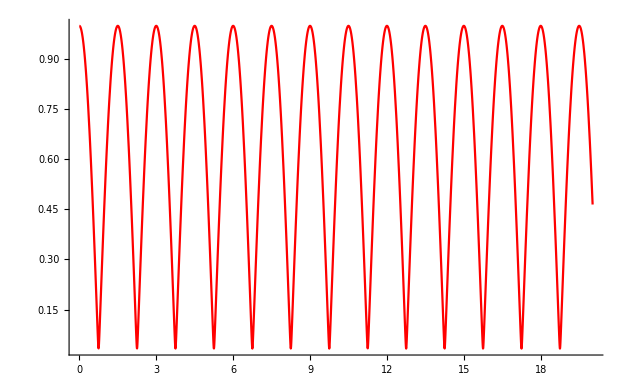

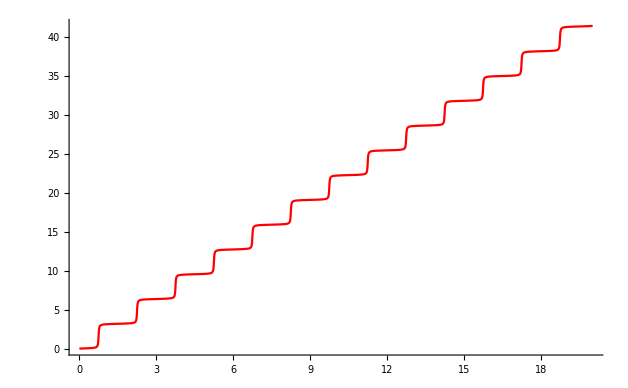

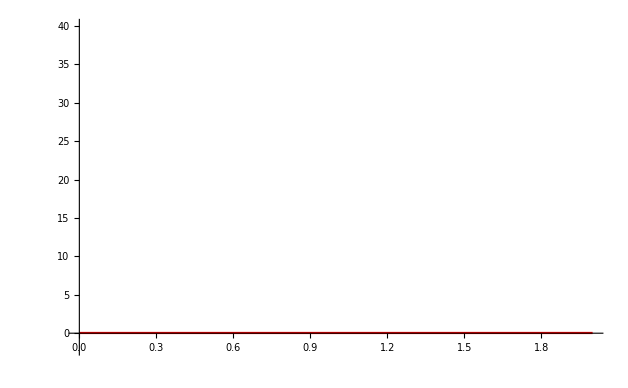

```mathematica
L=10
Subscript[l, 0]=2
α=0
m=0.1
g=10

s={D[(D[P,θ'[t]]), t]-D[P,θ[t]]==0,
D[(D[P,ϕ'[t]]), t]-D[P,ϕ[t]]==0}
ics={θ[0]== 1,θ'[0]== 0,ϕ[0]== 0,ϕ'[0]== 0.1}
sol=NDSolve[{s,ics},{θ,ϕ},{t,0,200}]
Plot[Evaluate[θ[t]/.sol],{t,0,20},PlotRange->All,PlotStyle->Red]
Plot[Evaluate[ϕ[t]/.sol],{t,0,20},PlotRange->All,PlotStyle->Red]
Plot[Evaluate[D[P,ϕ'[t]]/.sol],{t,0,2},PlotRange->{-2,40},PlotStyle->Red]
```

```mathematica
Remove[θ,ϕ]
```